```mathematica
Punto 1 
a) Desarrollo impar y par de la función f(x)=-x
```

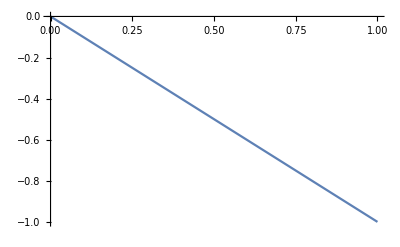

```mathematica
Plot[-x,{x,0,1}]
```

Desarrollo par

1

Piecewise[{{x, -1<x<0}, {-x, 0<x<1}, {0, True}}]

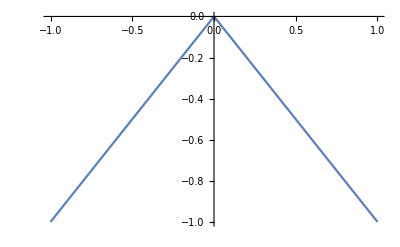

```mathematica
L=1
f[x_]=Piecewise[{{x,-L<x<0},{-x,0<x<L}}]
Plot[f[x],{x,-L,L}]
```

```mathematica
a0=1/(2 L) ∫_-L^L f[x]ⅆx;
a[n_]:=1/L ∫_-L^L f[x] Cos[(n π x)/L]ⅆx;
b[n_]:=1/L ∫_-L^L f[x] Sin[(n π x)/L]ⅆx;
t[x_,n_]=a[k] Cos[(n π x)/L]+b[n] Sin[(n π x)/L]+a0;
Print[a0]
Print[a[n]]
Print[b[n]]
g[x_,q_]:=∑_(k=1)^q t[x,n];
Manipulate[Plot[{f[x],g[x,p]},{x,-  L, L},Background->Black,AxesStyle->Red],{p,1,80}]
```

-1/2

-(2 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π^2)

0

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,1}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

```mathematica
Ahora compute
```